### Lab Calculations

```mathematica
a=3.5239;
λ=1.5418;
```

```mathematica
tohkl[hkl_]:=Table[Mod[⌊hkl/10^i⌋,10],{i,2,0,-1}]
Subscript[d, hkl_]:=a/(√Total[tohkl[hkl]^2])
```

```mathematica
Table[
{n,hkl,
#(θ/.Solve[n λ==2 Subscript[d, hkl] Sin[θ °],θ])&/@{1,2}
},
{n,1,3},
{hkl,{111,200,220,311,222,400,331,420,422}}
]//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

1 | 
111 | 
22.2661 | 44.5323 | 1 | 
200 | 
25.9462 | 51.8923 | 1 | 
220 | 
38.2254 | 76.4507 | 1 | 
311 | 
46.5151 | 93.0302 | 1 | 
222 | 
49.2722 | 98.5445 | 1 | 
400 | 
61.0513 | 122.103 | 1 | 
331 | 
72.4715 | 144.943 | 1 | 
420 | 
78.0529 | 156.106 | 1 | 
422 | 
90.-21.5718 ⅈ | 180.-43.1436 ⅈ
2 | 
111 | 
49.2722 | 98.5445 | 2 | 
200 | 
61.0513 | 122.103 | 2 | 
220 | 
90.-38.7468 ⅈ | 180.-77.4937 ⅈ | 2 | 
311 | 
90.-52.5602 ⅈ | 180.-105.12 ⅈ | 2 | 
222 | 
90.-55.9367 ⅈ | 180.-111.873 ⅈ | 2 | 
400 | 
90.-66.3992 ⅈ | 180.-132.798 ⅈ | 2 | 
331 | 
90.-72.2844 ⅈ | 180.-144.569 ⅈ | 2 | 
420 | 
90.-74.0019 ⅈ | 180.-148.004 ⅈ | 2 | 
422 | 
90.-79.989 ⅈ | 180.-159.978 ⅈ
3 | 
111 | 
90.-29.6303 ⅈ | 180.-59.2607 ⅈ | 3 | 
200 | 
90.-44.198 ⅈ | 180.-88.3961 ⅈ | 3 | 
220 | 
90.-70.4558 ⅈ | 180.-140.912 ⅈ | 3 | 
311 | 
90.-80.9836 ⅈ | 180.-161.967 ⅈ | 3 | 
222 | 
90.-83.7743 ⅈ | 180.-167.549 ⅈ | 3 | 
400 | 
90.-92.8113 ⅈ | 180.-185.623 ⅈ | 3 | 
331 | 
90.-98.0997 ⅈ | 180.-196.199 ⅈ | 3 | 
420 | 
90.-99.6653 ⅈ | 180.-199.331 ⅈ | 3 | 
422 | 
90.-105.19 ⅈ | 180.-210.38 ⅈ

```mathematica
VernierFormat2`VernierFormat2Import[filename_String,options___]:=Module[
{stream,head,data},
stream=OpenRead[filename];
head=ReadList[stream,"String",7];
data=Partition[ReadList[stream,"Number"],2];
Close[stream];
{
"Header"->head,
"Data"->data
}
]
```

```mathematica
ImportExport`RegisterImport[
"VernierFormat2",
VernierFormat2`VernierFormat2Import
]
```

```mathematica
hklLookupTable={{100, 110, 111, 200, 210, 211, {}, 220, {300,221}, 310, 311, 222, 320, 321, {}, 400, {410,322}, {411,330}, 331, 420, 421, 332, {}, 422, {500,430}}}[[1]];
Length@hklLookupTable
```

25

### Analysis

```mathematica
dataFiles=FileNames["*.txt",NotebookDirectory[]<>"XRayLab"]
data=Table[{StringSplit[FileNameSplit[path][[-1]],"."][[1]],Import[path,{"VernierFormat2","Data"}]},{path,dataFiles}];
```

{C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi160_0.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi54_40_Fine.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni18Cu82_48_43_Fine.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni47Cu53_48_43_Fine.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni74Cu26_50_43_Fine.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi100_70.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi130_120.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi160_140.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi55_40_Fine.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi60_40.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Silicon80_20.txt,C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\USNickel_50_43_Fine.txt}

```mathematica
fullSpeed=Table[!StringContainsQ[file,"Fine"],{file,dataFiles}];
slope=1/2+3/2 Boole@fullSpeed;
measurementAngles=Table[
ToExpression/@StringTrim[Take[StringSplit[StringSplit[FileNameSplit[file][[-1]],"."][[1]],"_"]/."Fine"|"det"->Nothing,-2],Except@DigitCharacter..],
{file,dataFiles}
];
minToAngle[i_][min_]:=measurementAngles[[i,1]]-slope[[i]]min
angles=Table[minToAngle[i]/@data[[i,2,;;,1]],{i,Length@data}];
data=Table[{data[[i,1]],{angles[[i]]/2,data[[i,2,;;,2]]}ᵀ},{i,Length@data}];
```

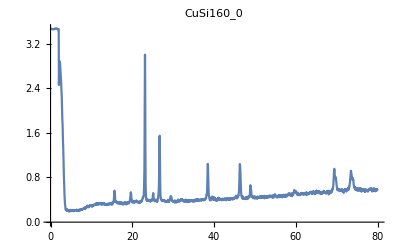
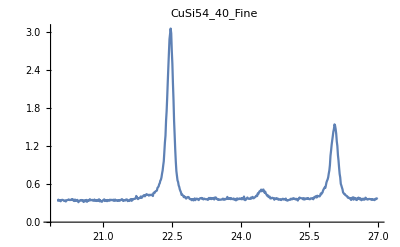
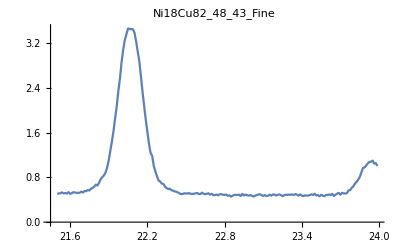
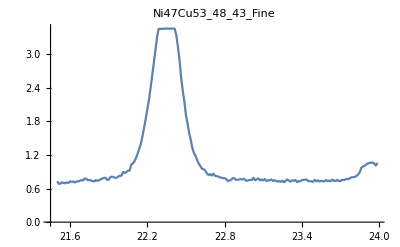
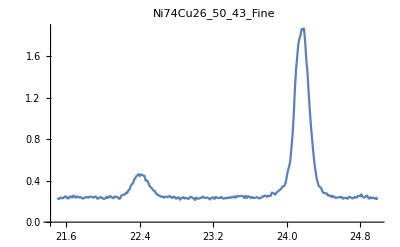
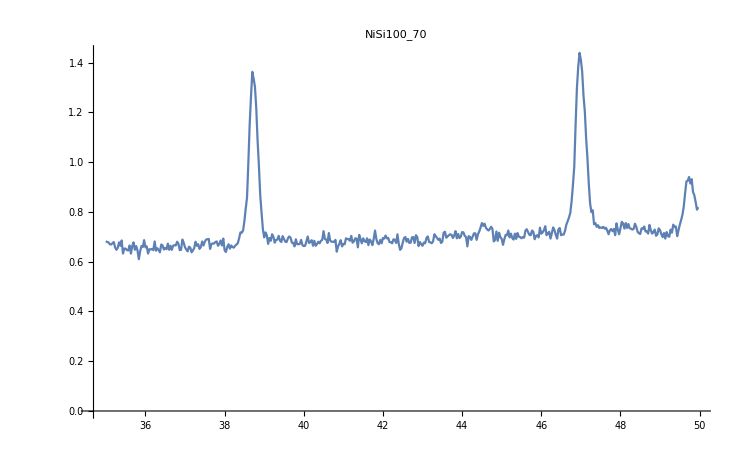
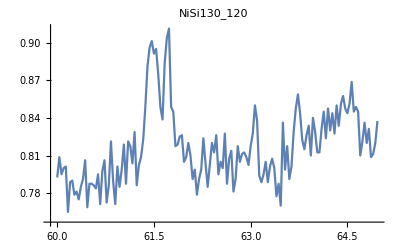
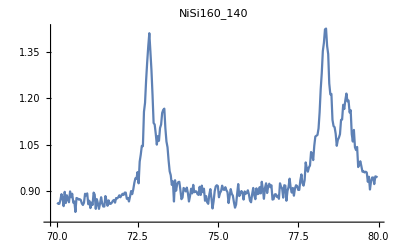

```mathematica
Table[ListPlot[datum[[2]],PlotLabel->datum[[1]],Joined->True,PlotRange->Full],{datum,data}]
```

#### Peak finding for each run

each run has different parameters needed to find all the peaks

```mathematica
peaks={{FindPeaks[data1[[;;,2]],1.5,0.01]}, {2}, {3}}
```

```mathematica
runData=data[[1,2]];
{runAngles,runVoltages}=runDataᵀ;
σ=5;
runVoltagesSmooth=GaussianFilter[runVoltages,{50,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
s=0.0006;
s=StandardDeviation@convolved/2.5
```

0.000970148

```mathematica
getAngles[data_,index_]:=;
getAngles[data_,indices_]:=;
```

```mathematica
{peakIdx,peakV}=FindPeaks[runVoltagesSmooth]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

```mathematica
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ
peakAngle=runAngles[[peakIdx]]
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

{{130,211,622,673,831,1011,1067,1098,1138,1207,1287,1548,1565},{0.00340093,0.00456808,0.00295845,0.00861857,0.00803176,0.00113221,0.0138333,0.00147948,0.026972,0.00235396,0.00277913,0.00655896,0.00668273}}

{73.5,69.45,48.9,46.35,38.45,29.45,26.65,25.1,23.1,19.65,15.65,2.6,1.74999}

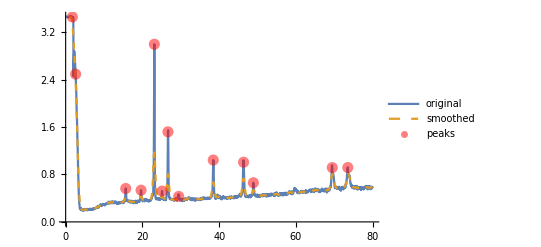

```mathematica
ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"original","smoothed","peaks"}
]
```

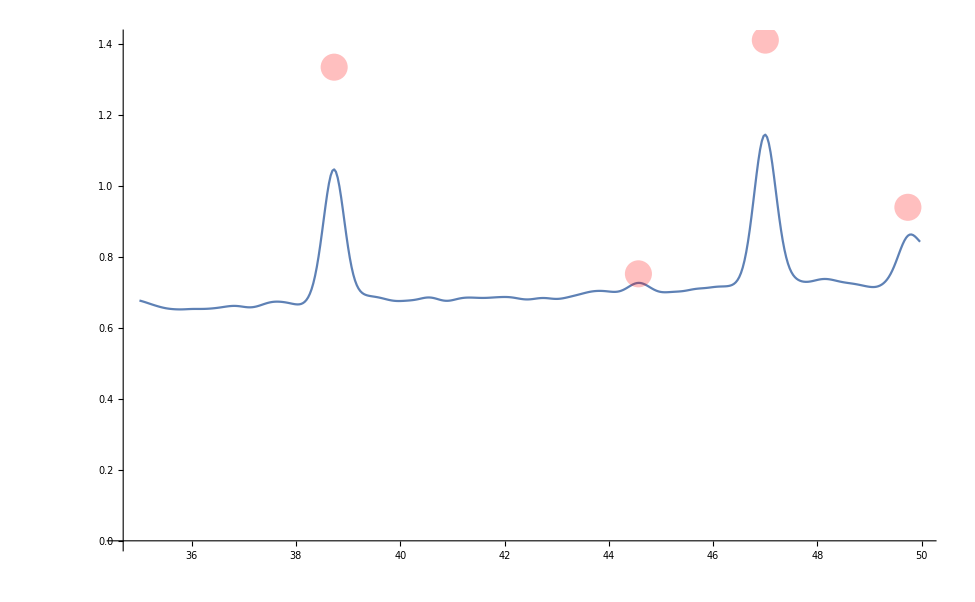

```mathematica
ListPlot[
{runDataSmooth,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.25]]},
PlotRange->Full
]
```

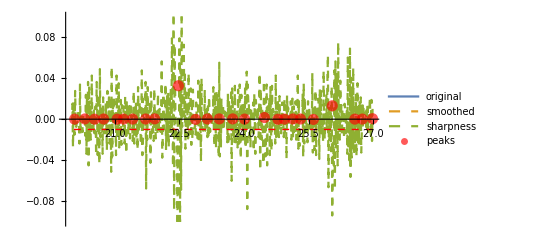

```mathematica
sharpness={runAngles,ListConvolve[{1,-2,1},ArrayPad[runVoltages,1,"Reversed"]]}ᵀ;
ListLinePlot[
{runData,runDataSmooth,sharpness,peaks},
Joined->{True,True,True,False},
PlotStyle->{Automatic,Dashed,Dashed,{Directive[Red,PointSize[.02],Opacity[0.65]]}},
PlotLegends->{"original","smoothed","sharpness","peaks"},
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-0.01},{runAngles[[-1]],-0.01}}]},
PlotRange->{-.1,.1}
]
```

0.000803246

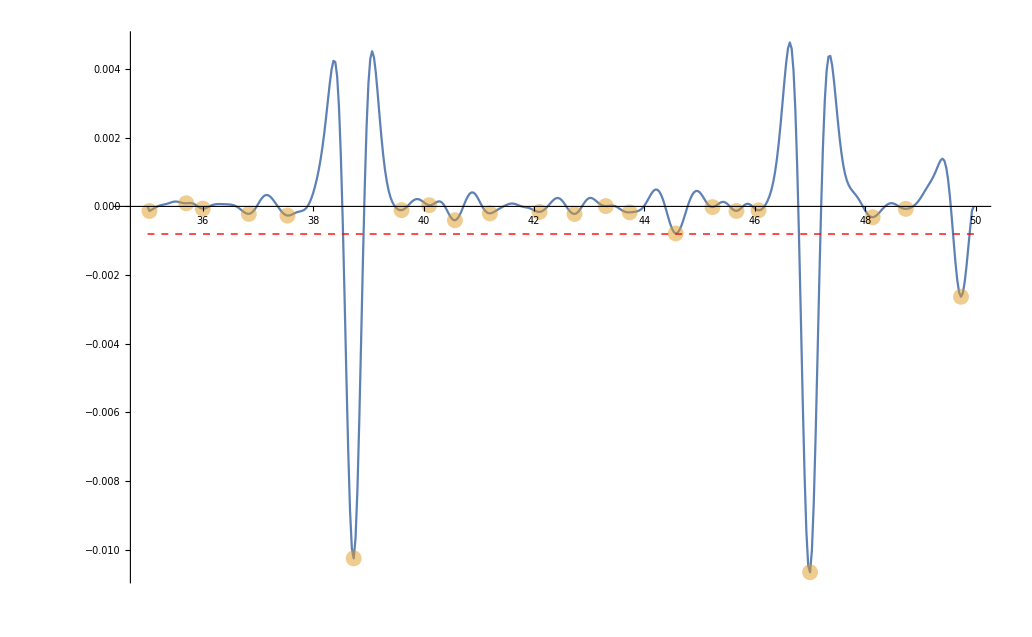

```mathematica
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation@convolved/2.5
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

```mathematica
data1[[2]]
```

{26.975,0.37375}

```mathematica
GaussianFilter[data1[[2]],{3,1.5}]
```

{17.5865,9.76229}